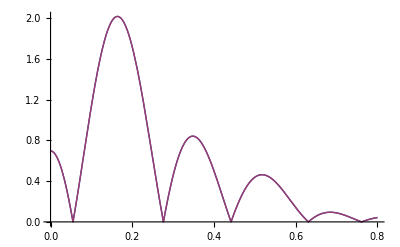
file This^3 -Graphics-^4

```mathematica
(*This file compares two different ways of calculating the X-ray form factor. One method follows from SIMtoEXP, in which electron density profile from a sim file is integrated in a discrete fashion. The second method interpolates the electron density profile, which is discrete, and performs a numerical integration using NIntegrate. The comparison of the calculated form factors shows that both methods produce the same form factor, except some small differences. It proves that SIMtoEXP way is good enough. *)
```

```mathematica
mydata=ReadList["dopc-tat2-a70-0.edp",Number,RecordLists->True]
```

{{-34.5,0.32593},{-33.5,0.32552},{-32.5,0.32662},{-31.5,0.32752},{-30.5,0.32512},{-29.5,0.32586},{-28.5,0.32739},{-27.5,0.32723},{-26.5,0.32842},{-25.5,0.33021},{-24.5,0.33722},{-23.5,0.3452},{-22.5,0.35881},{-21.5,0.37896},{-20.5,0.401},{-19.5,0.41907},{-18.5,0.42891},{-17.5,0.42851},{-16.5,0.41522},{-15.5,0.40038},{-14.5,0.38652},{-13.5,0.36293},{-12.5,0.34505},{-11.5,0.33084},{-10.5,0.31627},{-9.5,0.30739},{-8.5,0.30036},{-7.5,0.29793},{-6.5,0.2897},{-5.5,0.28589},{-4.5,0.28047},{-3.5,0.27668},{-2.5,0.26669},{-1.5,0.26457},{-0.5,0.25932},{0.5,0.26139},{1.5,0.26212},{2.5,0.26785},{3.5,0.27575},{4.5,0.28288},{5.5,0.28679},{6.5,0.29029},{7.5,0.29251},{8.5,0.29722},{9.5,0.30252},{10.5,0.31298},{11.5,0.32687},{12.5,0.34533},{13.5,0.36771},{14.5,0.38965},{15.5,0.41345},{16.5,0.42824},{17.5,0.43069},{18.5,0.42539},{19.5,0.41783},{20.5,0.39962},{21.5,0.37837},{22.5,0.35866},{23.5,0.34234},{24.5,0.33558},{25.5,0.33056},{26.5,0.32838},{27.5,0.32879},{28.5,0.32683},{29.5,0.32504},{30.5,0.32776},{31.5,0.32514},{32.5,0.32611},{33.5,0.32598},{34.5,0.32559}}

```mathematica
func[q_]:=test⟦All,2⟧.Cos[q*test⟦All,1⟧]
```

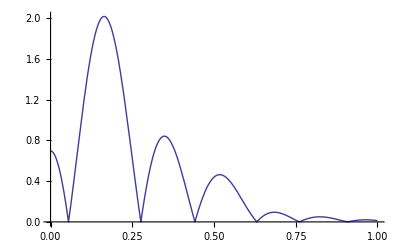

```mathematica
Plot[Abs[func[q]],{q,0,1}]
```

```mathematica
Total[test⟦All,2⟧*Cos[z*q]]
```

0.69592

```mathematica
Total[{1,2,3}]
```

6

```mathematica
test=Transpose[{mydata⟦All,1⟧,mydata⟦All,2⟧-.326}]
```

{{-34.5,-0.00007},{-33.5,-0.00048},{-32.5,0.00062},{-31.5,0.00152},{-30.5,-0.00088},{-29.5,-0.00014},{-28.5,0.00139},{-27.5,0.00123},{-26.5,0.00242},{-25.5,0.00421},{-24.5,0.01122},{-23.5,0.0192},{-22.5,0.03281},{-21.5,0.05296},{-20.5,0.075},{-19.5,0.09307},{-18.5,0.10291},{-17.5,0.10251},{-16.5,0.08922},{-15.5,0.07438},{-14.5,0.06052},{-13.5,0.03693},{-12.5,0.01905},{-11.5,0.00484},{-10.5,-0.00973},{-9.5,-0.01861},{-8.5,-0.02564},{-7.5,-0.02807},{-6.5,-0.0363},{-5.5,-0.04011},{-4.5,-0.04553},{-3.5,-0.04932},{-2.5,-0.05931},{-1.5,-0.06143},{-0.5,-0.06668},{0.5,-0.06461},{1.5,-0.06388},{2.5,-0.05815},{3.5,-0.05025},{4.5,-0.04312},{5.5,-0.03921},{6.5,-0.03571},{7.5,-0.03349},{8.5,-0.02878},{9.5,-0.02348},{10.5,-0.01302},{11.5,0.00087},{12.5,0.01933},{13.5,0.04171},{14.5,0.06365},{15.5,0.08745},{16.5,0.10224},{17.5,0.10469},{18.5,0.09939},{19.5,0.09183},{20.5,0.07362},{21.5,0.05237},{22.5,0.03266},{23.5,0.01634},{24.5,0.00958},{25.5,0.00456},{26.5,0.00238},{27.5,0.00279},{28.5,0.00083},{29.5,-0.00096},{30.5,0.00176},{31.5,-0.00086},{32.5,0.00011},{33.5,-0.00002},{34.5,-0.00041}}

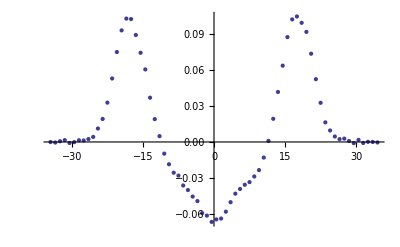

```mathematica
ListPlot[test]
```

```mathematica
f=Interpolation[test]
```

InterpolatingFunction[{{-34.5,34.5}},<>]

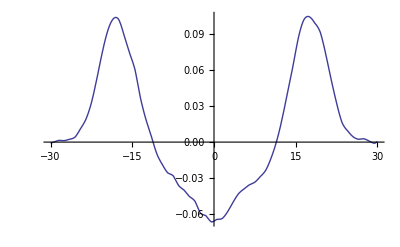

```mathematica
Plot[f[x],{x,-30,30}]
```

```mathematica
FF[q_]:=NIntegrate[f[z]*Cos[z*q],{z,-34.5,34.5},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->30,PrecisionGoal->4]
```

```mathematica
Plot[{Abs[FF[q]],Abs[func[q]]},{q,0,0.8}]
```

-Graphics-

```mathematica
edp⟦1⟧
edp⟦1,1⟧
edp[[1,1]]
```

{-34.826,-0.00007}

-34.826

-34.826